```mathematica
F[x0]:=x0*Integrate[BesselK[5/3,x],{x,x0,Infinity},Assumptions->{x>0,x0>0},GenerateConditions->False]
```

```mathematica
Fre[x0]:=Re[x0*Integrate[BesselK[5/3,x],{x,x0,Infinity},Assumptions->{x>0,x0>0},GenerateConditions->False]]
```

```mathematica
F[0.29]
```

0.917985+1.28196×10^-16 ⅈ

```mathematica
F[xg]
```

xg If[xg>0,(2^(2/3) Gamma[2/3] HypergeometricPFQ[{-1/3},{-2/3,2/3},xg^2/4])/xg^(2/3)+(π (-320+(81 2^(1/3) xg^(8/3) HypergeometricPFQ[{4/3},{7/3,8/3},xg^2/4])/Gamma[-1/3]))/(320 √3),Integrate[BesselK[5/3,x],{x,xg,∞},Assumptions→xg≤0]]

```mathematica
IntBs53=FullSimplify[(2^(2/3) Gamma[2/3] HypergeometricPFQ[{-1/3},{-2/3,2/3},xg^2/4])/xg^(2/3)+(π (-320+(81 2^(1/3) xg^(8/3) HypergeometricPFQ[{4/3},{7/3,8/3},xg^2/4])/Gamma[-1/3]))/(320 √3),{xg>0}]
```

(2^(2/3) Gamma[2/3] HypergeometricPFQ[{-1/3},{-2/3,2/3},xg^2/4])/xg^(2/3)+(π (-320+(81 2^(1/3) xg^(8/3) HypergeometricPFQ[{4/3},{7/3,8/3},xg^2/4])/Gamma[-1/3]))/(320 √3)

```mathematica
xg*IntBs53//.{xg->0.29}
```

0.917985

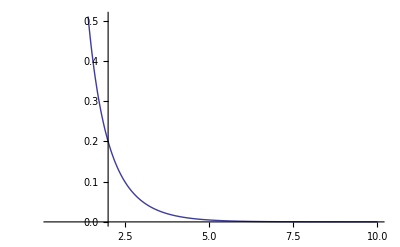

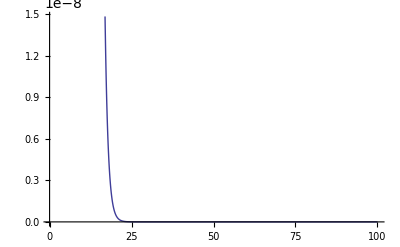

```mathematica
Plot[BesselK[5/3,x],{x,0.29,10}]
Plot[BesselK[5/3,x],{x,0.29,100}]
```

```mathematica
F[x0_?NumericQ]:=x0*NIntegrate[BesselK[5/3,x],{x,x0,Infinity}]
```

```mathematica
F[0.29]
```

0.917985

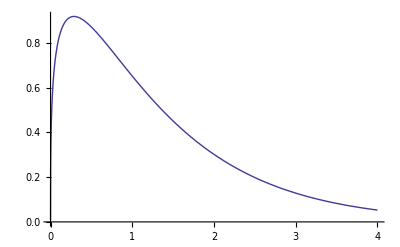

```mathematica
Plot[F[x],{x,0,4}]
```

```mathematica
Clear[x]
myIntFxraw=Integrate[F[x],{x,0,Infinity},GenerateConditions->False]
```

(8 π)/(9 √3)

```mathematica
N[myIntFxraw]
```

1.61227

```mathematica
mu=0
intFxraw=2^(mu+1)/(mu+2)*Gamma[mu/2+7/3]*Gamma[mu/2+2/3]
```

0

Gamma[2/3] Gamma[7/3]

```mathematica
N[intFxraw]
```

1.61227

```mathematica
Sqrt[3]/(2*Pi)*1.0
```

0.275664

```mathematica
wc=3*gam^2*q*B*Sin[al]/(2*m*c)
intFx=myIntFxraw*wc
Pw=Sqrt[3]*q^3*B*Sin[al]/(2*Pi*m*c^2)*intFx
P=2*q^4*B^2*(gam^2-1)*Sin[al]^2/(3*m^2*c^3)
```

(3 B gam^2 q Sin[al])/(2 c m)

(4 B gam^2 π q Sin[al])/(3 √3 c m)

(2 B^2 gam^2 q^4 Sin[al]^2)/(3 c^3 m^2)

(2 B^2 (-1+gam^2) q^4 Sin[al]^2)/(3 c^3 m^2)

```mathematica
P/Pw
N[%]
```

(-1+gam^2)/gam^2

(-1.+gam^2)/gam^2

```mathematica
x0=0.29;
x0*Integrate[BesselK[5/3,x],{x,x0,10000}]
```

1.44395

```mathematica
x0=0.29;
x0*NIntegrate[BesselK[5/3,x],{x,x0,Infinity}]
```

0.917985

```mathematica
Plot[F[x],{x,0,4}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.00008171428571428571`, 0.00008171428571428571`, ∞}.

NIntegrate::itraw: Raw object 0.0000817143 cannot be used as an iterator.

Integrate::ilim: Invalid integration variable or limit(s) in {0.08171436734693877`, 0.08171436734693877`, ∞}.

NIntegrate::itraw: Raw object 0.0817144 cannot be used as an iterator.

Integrate::ilim: Invalid integration variable or limit(s) in {0.16334702040816323`, 0.16334702040816323`, ∞}.

General::stop: Further output of Integrate will be suppressed during this calculation.

NIntegrate::itraw: Raw object 0.163347 cannot be used as an iterator.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

-Graphics-